# Задание 08.

## Метод обратной функции распределения. Двумерное случайное блуждание

## ФИО, № группы

## Задача

В начальный момент времени частица оказывается в точке (0,0), двигаясь вдоль положительного направления оси x (θ_0=0). Частица либо поглощается с вероятностью p, и на этом ее траектория обрывается, либо с вероятностью (1-p) рассеивается на некоторый угол θ (относительно предыдущего направления движения) с вероятностью
P(θ)∝ cos^3 θ, -π/2≤θ≤π/2,
т.е. новое направление движения пересчитывается по формуле θ_(n+1)=θ_n+θ, 

Если частица рассеялась, то она перемещается на расстояние L вдоль нового направления движения, причем вероятность данного значения L
определяется длиной свободного пробега λ:
P(L) ∝ e^(-L/λ), L≥0

Используя метод обратной функции распределения запрограммируйте

генератор genL, который при каждом вызове возвращает случайное значения для расстояния, на которое перемещается частица, при заданном значении длины свободного пробега lambda. (параметр lambda можно принимать и сохранять в конструкторе init[genL, lambda])

генератор genTheta, который возвращает случайное значение для угла рассеяния

в качестве базового генератора случайных чисел, равномерно распределенных от нуля до единицы, можно использовать RandomReal[].

Cгенерируйте достаточное количество случайных значений, постройте гистограммы для расстояний и углов, сравните с ожидаемыми плотностями распределений

-Graphics-

Напишите функцию trajectory[p, genL, genTheta], которая принимает вероятность обрыва траектории и имена генераторов расстояния и угла рассеяния и возвращает траекторию движения частицы. В реализации также могут быть полезны инструменты для работы с повторяющимися применениями функций (Applying Functions Repeatedely)

```mathematica
trajectory[0.1,genL,genTheta] (* генератор genL использует lambda = 1.0 *)
```

{{0,0},{0.922611,0.},{2.38996,-2.40254},{2.60577,-2.60678},{2.94296,-2.79911},{2.96759,-2.82337},{3.20167,-2.92143},{3.45297,-2.99513}}

Нарисуйте несколько траекторий

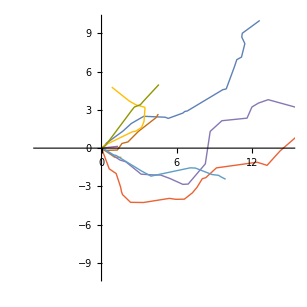

При заданных lambda и p оцените среднее значение глубины проникновения вдоль оси х по набору траекторий